# 2 Mar 2017 NW GaAs mesa 1200/100 and 1200/65

```mathematica
ClearAll[mar2]
mar2=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\mar\\2\\2mar_accun_"<>ToString[i]<>".dat"],{i,1,19}];
```

```mathematica
ClearAll[allDat,short1200100,long1200100]
short1200100 = {"short1200100",mar2[[{1,4,5,8,9}]]};
long1200100 = {"long1200100",mar2[[{2,3,6,7,10}]]};
allDat={short1200100,long1200100};
```

```mathematica
ClearAll[powerDatDict]
powerDatDict = 
<|
"short1200100"->{0.25,0.5,1,2,4},
"long1200100"->{0.25,0.5,1,2,4}
|>;
```

```mathematica
TableForm[Table[Table[allDat[[j]][[2,i]][[1,1]],{i,Length[allDat[[j,2]]]}],{j,Length[allDat]}]]
```

-101.5 | -101.5 | -101.5 | -101.5 | -101.5
-101. | -101. | -101. | -101. | -101.

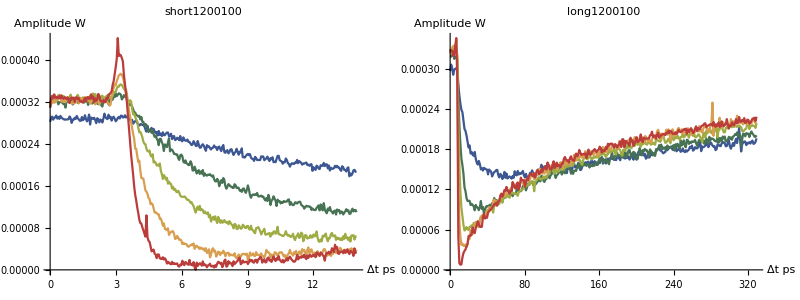

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
Table[dat[[2,i]][[All,{3,2}]],{i,1,Length[dat[[2]]]}],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->dat[[1]],
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All],
{dat,allDat}],
2]
]
```

```mathematica
amplitudes=
Table[
{
dat[[1]],
Table[
MeanFilter[
(dat[[2]][[i,All,2]]+(Max[Mean/@dat[[2]][[All,2;;4,2]]]-Mean[dat[[2]][[i,2;;4,2]]]))/Mean/@Max[dat[[2]][[All,2;;4,2]]],
1],
{i,1,Length[dat[[2]]]}]
},
{dat,allDat}];
```

```mathematica
normDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],amplitudes[[i,2]][[j]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

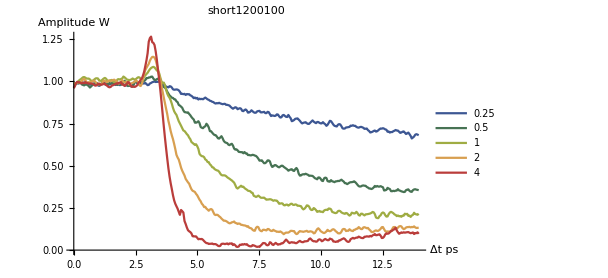
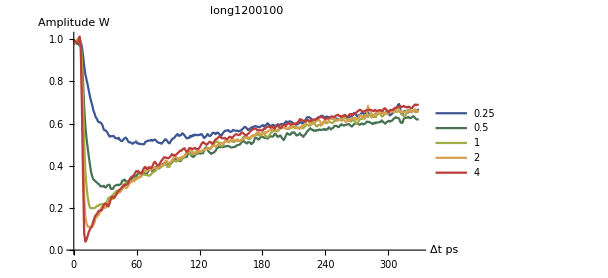
-Graphics- | -Graphics-

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
normDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict[name]],
{name,Keys[powerDatDict]}],
2]
]
```

```mathematica
normLogDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat[[i,2]][[j,All,3]],Log[amplitudes[[i,2]][[j]]]}],
{j,Length[allDat[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

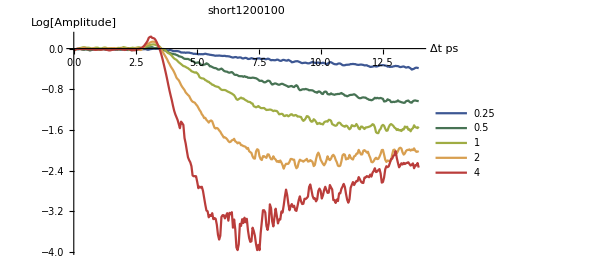
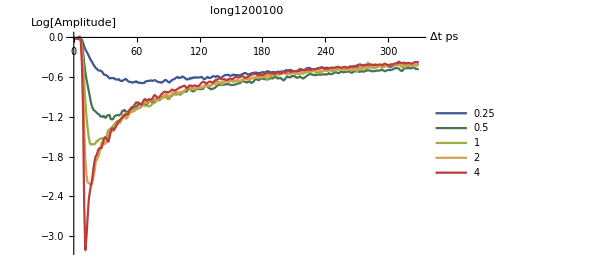
-Graphics- | -Graphics-

```mathematica
TableForm[
Partition[
Table[
ListLinePlot[
normLogDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Log[Amplitude]"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict[name]],
{name,Keys[powerDatDict]}],
2]
]
```

Short dynamic

#### short1200100

```mathematica
Keys[powerDatDict]
```

{short1200100,long1200100}

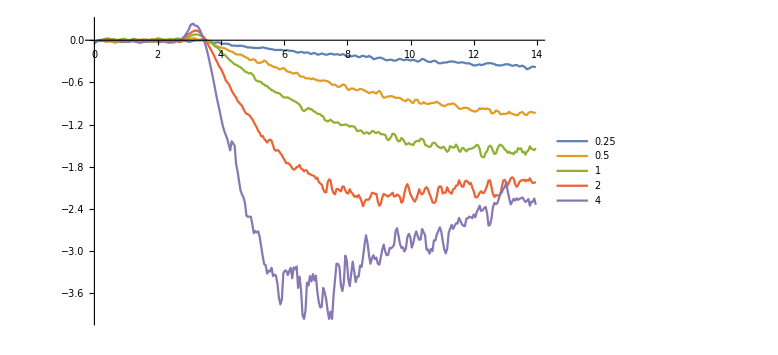

```mathematica
ListLinePlot[normLogDatDic["short1200100"],PlotLegends->powerDatDict["short1200100"],ImageSize->Large]
```

Linear area for this sample

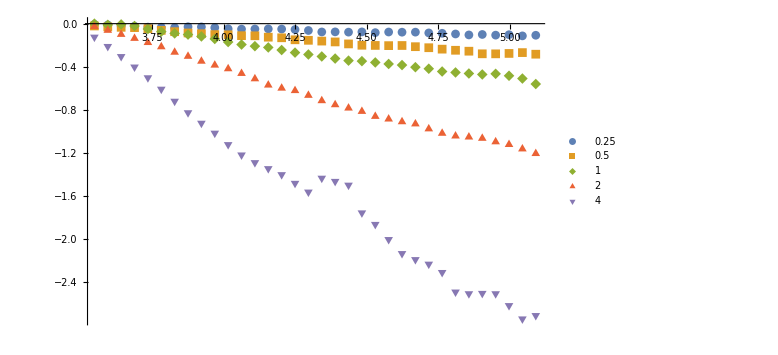

```mathematica
ListPlot[normLogDatDic["short1200100"][[All,77;;110]],PlotLegends->powerDatDict["short1200100"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShort1200100 = normLogDatDic["short1200100"][[;;,77;;110]];
```

```mathematica
lineCoefShort1200100 = Table[FindFit[lineEreaShort1200100[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShort1200100]}];
```

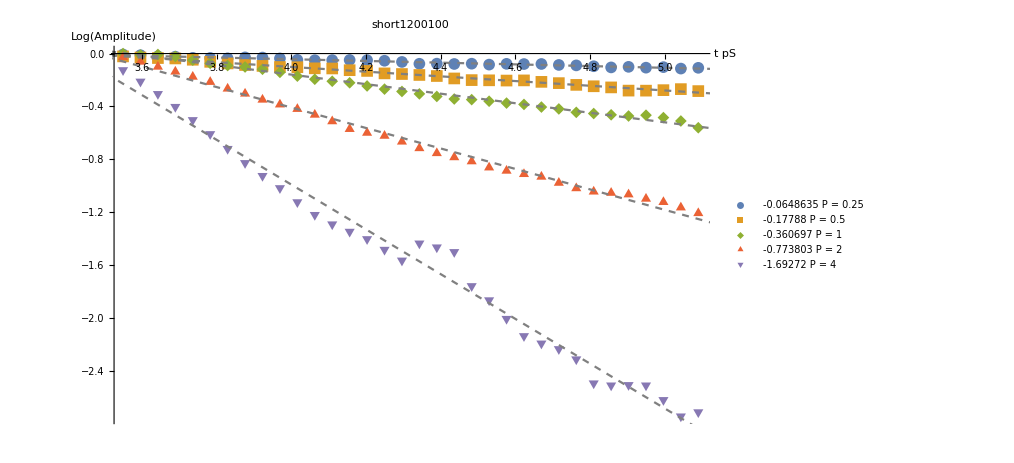

```mathematica
Show[
ListPlot[
Table[lineEreaShort1200100[[i]],{i,1,5}],
PlotLegends->Table[ToString[lineCoefShort1200100[[i,1,2]]]<>"    P = "<>ToString[powerDatDict["short1200100"][[i]]],{i,1,5}],
ImageSize->750,
PlotLabel->"short1200100",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShort1200100[[i]],{i,1,5}],
{x,3.2,5.3},
PlotStyle->{Gray,Dashed}
]
]
```

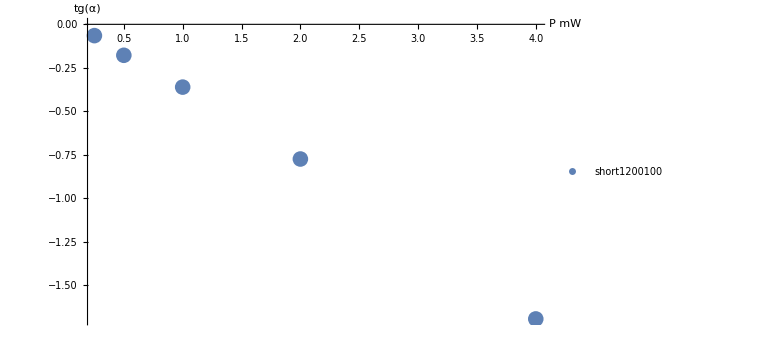

```mathematica
ListPlot[{
Sort[Table[{powerDatDict["short1200100"][[i]],lineCoefShort1200100[[i,1,2]]},{i,1,5}]]},
PlotRange->All,
PlotLegends->{"short1200100"},
LabelStyle->{Black,16},
ImageSize->Large,
AxesLabel->{"P mW","tg(α)"},
PlotMarkers->{Automatic,16}
]
```